```mathematica
b={0,0.1,0.3,0.5,0.7,0.9,1.1,1.3};
bstring={"0","0p1","0p3","0p5","0p7","0p9","1p1","1p3"};

s={15,FontFamily->"Times New Roman"};
```

```mathematica
data={};
bdy=12;
x=N@Range[-bdy*0.7,bdy*0.7,2 bdy*0.7/200] 10^-6;
Do[ 
file=NotebookDirectory[]<>"dIdV22mK"<>bstring[[i]]<>"mT.DAT";
a=Sort@Select[Import[file,"Table",HeaderLines->1],Abs[#[[1]]]<bdy 10^-6&];
a=Mean /@ GatherBy[a, First];

f=Interpolation[a,InterpolationOrder->1];
a=MovingAverage[Transpose@{x 10^6,Table[b[[i]],Length@x],f[x]},15];
If[i==1,mm=Max[(Transpose@a)[[3]]];,];
a=Map[#{1,1,4/mm}&,a];

(*a = Map[{b[[i]],#[[1]] 10^6,#[[2]]*4/mm}&,a];*)
AppendTo[data,a];
,
{i,Length@b}]
data=ArrayFlatten[data,1];
data2=Map[{1,-1,1}#&,data];
datacombined=ArrayFlatten[{data,data2},1];
```

```mathematica
ListPlot3D[datacombined,PlotRange->All,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

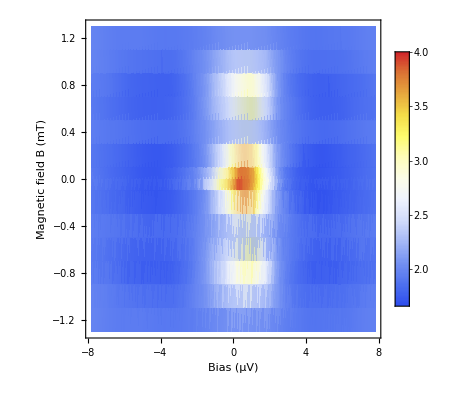

```mathematica
l4=ListDensityPlot[datacombined,
ColorFunction->"TemperatureMap",PlotRange->All,
LabelStyle->Directive[15],
Axes->False,
FrameLabel->{Style["Bias (μV)",s],Style["Magnetic field B (mT)",s]},
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],PlotLegends->Automatic
]
```

```mathematica
Export[NotebookDirectory[]<>"..\mag.pdf",l4]
```

C:\Users\rafae\Documents\ZBCP poster\fig\B_dependence\..\mag.pdf

### Fit

```mathematica
fraunhofer[x_]:=Abs[Sin[π 2 x]/(π 2 x)];
```

```mathematica
datafit={};
bdy=12;
x=N@Range[-bdy*0.7,bdy*0.7,2 bdy*0.7/200] 10^-6;
file=NotebookDirectory[]<>"dIdV22mK"<>bstring[[1]]<>"mT.DAT";
a=Sort@Select[Import[file,"Table",HeaderLines->1],Abs[#[[1]]]<bdy 10^-6&];
a=Mean /@ GatherBy[a, First];

f=Interpolation[a,InterpolationOrder->1];
a=MovingAverage[f[x],15];
a=a/Max[a]*4-2;
x=MovingAverage[x,15]*10^6;
res=28;
bval=Table[k,{k,-Max[b],Max[b],2 Max[b]/(res-1)}];
factor=fraunhofer[bval];
bvalr=ArrayFlatten[Transpose@Table[bval,Length@x],1];
xr=ArrayFlatten[Table[x,res],1];
ar=ArrayFlatten[(Transpose@{factor}).{a},1];
datafit=Transpose@{xr,bvalr,ar+2};
```

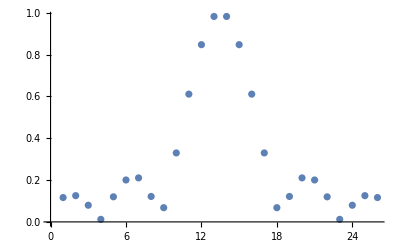

```mathematica
ListPlot[factor]
```

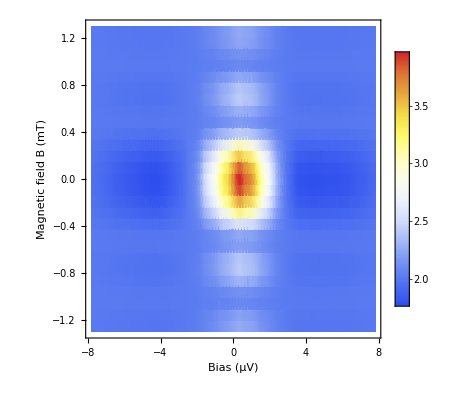

```mathematica
l6=ListDensityPlot[datafit,
ColorFunction->"TemperatureMap",PlotRange->All,
LabelStyle->Directive[15],
Axes->False,
FrameLabel->{Style["Bias (μV)",s],Style["Magnetic field B (mT)",s]},
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],PlotLegends->Automatic
]
```

```mathematica
Export[NotebookDirectory[]<>"..\mag_fit.pdf",l6]
```

C:\Users\rafae\Documents\ZBCP poster\fig\B_dependence\..\mag_fit.pdf

```mathematica
BesselI
```